449 Midterm
Megan Tabbutt
4/6/18

```mathematica
Import["/Users/megantabbutt/Desktop/Quantum/Defs/448defs.m"]
```

Each problem is worth the same. The usual take-home rules apply, in particular no discussing this with any other humans. Due 8 am Friday April 6. Hand in electronically, maximum of one .nb and one pdf file. I reserve the right to deduct points for answers that are difficult to read.

## 1) Sr has 2 valence electrons. Some of its important low-lying excited states are denoted 5s 5p ^3 P_j.

a) What are the possible values of j?

^3 P_j = ^(2S+1)L_j 	--> 	S = 1,   L = 1 

J = L + S 			-->	 	Addition of Ang Mom: 			j = 0, 1, 2. 

(Citation: Townsend Ch 3)

The possible values of j: 	     j = 0, 1, 2.

b) Let your largest answer to a) be j_max. Assuming the radial wavefunctions are P_(5s)(r) and P_(5p)(r), write down the total wavefunction for the state with j = m = j_max.

j_max = 2 . 			j = m = j_max 	 j = L + S, 			j = 2,  m=2,  L = 1,   S = 1

Individual Wavefunctions for the electrons is given by: 		ψ(r, θ, ϕ)=(P(r))/r Σ_(m_l m_s)C_(L m_l Sm_s)^(J m)Y_(L m_l)(θ,ϕ)m_s
The total wave function is given by: 	ψ_total =( Σ_(m_l m_s)C_(L m_l Sm_s)^(J m) )ψ_1 ψ_2 χ_ms   , 		where now the CG coefficient is for the total QM# 

The Clebsch-Gordon Coefficients are given by:	 Σ_(m_l m_s)C_(L m_l Sm_s)^(J m)  = Σ_(m_l m_s)C_(1 m_l 1 m_s)^(2 2) 	Because of selection rules, the only nonzero CG is the C_(1 111)^(2 2) . Selection Rules: 	m = ml + ms = 2. 	L = 1  -->   ml = -1, 0, 1 	Similarly, 		S = 1  -->   ms = -1, 0, 1 	Thus, ml and ms have to both be 1 to satisfy the condition on m. This is also apparent from the fact that we have chosen the maximal J and mj states, so there is only one combination of ml and ms to get this. 

ψ_1 and ψ_2 are the individual wavefunctions for the elections given by:

ψ_1(r_1, θ_1, ϕ_1)=(P_(5s)(r_1))/r_1 Y_(L_1 m_l_1)(θ_1,ϕ_1) = ψ_1(r_1, θ_1, ϕ_1)=(P_(5s)(r_1))/r_1 Y_(0 0)(θ_1,ϕ_1)
ψ_2(r_2, θ_2, ϕ_2)=(P_(5p)(r_2))/r_2 Y_(L_2 m_l_2)(θ_2,ϕ_2) = ψ_2(r_2, θ_2, ϕ_2)=(P_(5p)(r_2))/r_2 Y_(1 1)(θ_2,ϕ_2)

ψ_total =( Σ_(m_l m_s)C_(L m_l Sm_s)^(J m) )ψ_1 ψ_2 χ_ms   = 	C_(1 111)^(2 2) (P_(5s)(r_1))/r_1 Y_(0 0)(θ_1,ϕ_1)(P_(5p)(r_2))/r_2 Y_(1 1)(θ_2,ϕ_2) χ_ms = 1(P_(5s)(r_1))/r_1 Y_(0 0)(θ_1,ϕ_1)(P_(5p)(r_2))/r_2 Y_(1 1)(θ_2,ϕ_2))χ_1

ψ_total = ((P_(5s)(r_1))/r_1 Y_00(θ_1,ϕ_1))((P_(5p)(r_2))/r_2 Y_11(θ_2,ϕ_2)) χ_1

(Citation: Prof Walker’s Atomic State Notebook)

ψ_total = ((P_(5s)(r_1))/r_1 Y_00(θ_1,ϕ_1))((P_(5p)(r_2))/r_2 Y_11(θ_2,ϕ_2)) χ_1

c) Simplify: 5s 5p  ^3 P_jmax 1/r_12 5s 5p  ^3 P_jmax=

5s 5p  ^3 P_jmax 1/r_12 5s 5p  ^3 P_jmax= ∫_0^∞ ∫_0^∞ ((P_(5s)(r_1))/r_1)^2 1/r_12((P_(5p)(r_2))/r_2)^2 r_1^2 r_2^2 ⅆ r_1ⅆ r_2∫_0^π ∫_0^(2 π) (Y_00(θ_1,ϕ_1))^*Y_00(θ_1,ϕ_1)Sin[θ_1]ⅆ θ_1ⅆ ϕ_1∫_0^π ∫_0^(2 π) (Y_11(θ_2,ϕ_2))^*(Y_11(θ_2,ϕ_2))Sin[θ_2]ⅆ θ_2ⅆ ϕ_2

```mathematica
Angular1 = Integrate[(SphericalHarmonicY[0, 0, Subscript[θ, 1], Subscript[ϕ, 1]])^2 Sin[Subscript[θ, 1]], {Subscript[θ, 1],0,π}, {Subscript[ϕ, 1],0,2 π}]
```

1

```mathematica
Angular2 = Integrate[Conjugate[(SphericalHarmonicY[1, 1, Subscript[θ, 2], Subscript[ϕ, 2]])](SphericalHarmonicY[1, 1, Subscript[θ, 2], Subscript[ϕ, 2]])Sin[Subscript[θ, 2]], {Subscript[θ, 2],0,π}, {Subscript[ϕ, 2],0,2 π}]
```

1

∫_0^∞ ∫_0^∞ ((P_(5s)(r_1))/r_1)^2 1/r_12((P_(5p)(r_2))/r_2)^2 r_1^2 r_2^2 ⅆ r_1ⅆ r_2(1)(1) = ∫_0^∞ ∫_0^∞ P_(5s)(r_1)^2 1/r_12 P_(5p)(r_2)^2 ⅆ r_1ⅆ r_2

 (Citation: Prof Walker’s H21s2s Notebook and Townsend 9.9)

5s 5p  ^3 P_jmax 1/r_12 5s 5 p^3 P_jmax=  ∫_0^∞ ∫_0^∞ P_(5s)(r_1)^2 1/r_12 P_(5p)(r_2)^2 ⅆ r_1ⅆ r_2

## 2) A spin-0 particle with charge q = | e | and mass M moves in the spherically symmetric potential V(r) =  0 | r<a ∞ | r>a. The energy levels can be parameterized by the equation E_nl = (π^2 ℏ^2)/(2 M a^2)(n + δ_l)^2, where n is the number of radial zero crossings and δ_l depends, to a good approximation, mostly on l but only slightly on n.)

a) For s-states, the equation is exact. What is the value of δ for s-states?

s states have l = 0 

For a spherical potential we have that the solutions are spherical Bessel functions. Energy eigenvalues are determined by: j_l(k a)=0. (Townsend 10.70). Thus for the s states, where l = 0, we need the zeroth spherical Bessel function to be zero at a, and so we  need to find the first zero of the zeroth spherical Bessel function.

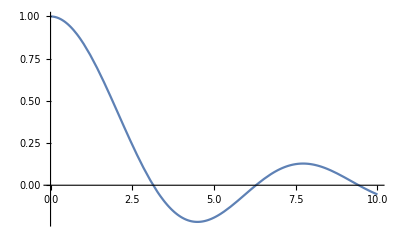

```mathematica
Plot[SphericalBesselJ[0, x], {x, 0, 10}]
```

```mathematica
FindRoot[SphericalBesselJ[0, x], {x, 2, 4}]
```

{x→3.14159}

The first zero of the zeroth Spherical Bessel Function is  at x = π. 

j_0(k r) = 0 = Sin[k r]/(k r), 	but x = k r = pi to satisfy this , 	in fact k r = n π will satisfy this equation. 	

Following a similar procedure to 10.4: 	k = Sqrt[(2 M E)/ℏ^2]  -- > 	E = (ℏ^2 k^2)/(2 M)

But we just found for the l = 0 case: 	k = (n π)/r

Thus for the s states:  	E_n0 = ℏ^2/(2 M)((π^2 n^2)/r^2),    r = a,  so we know that  E_n0 = ℏ^2/(2 M)((π^2 n^2)/a^2).

We want to find the value of δ_(l=0) though, so we need to solve these two equations: 	E_(nl=0) = (π^2 ℏ^2)/(2 M a^2)(n + δ_l)^2 = ℏ^2/(2 M)((π^2 n^2)/a^2). 

Clearly δ_l = 0.

(Citation: Townsend 10.4 and Griffiths example 4.1)

So we can see that δ_l = 0  for the s states.

b) Put δ0, δ1, and δ2 in numerical order. Briefly explain your reasoning.

As l increases a higher percentage of the total energy comes from the angular momentum, and thus delta is increasing with increasing l. This makes sense becuase there is an effective potential, and in the same way that the Hydrogen atom’s energy levels depend on l, ours do too.

δ_0 < δ_1 < δ_2

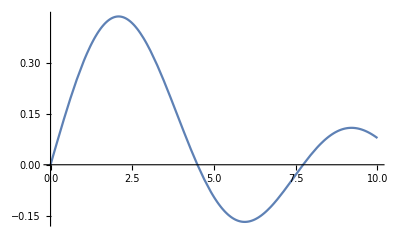

```mathematica
Plot[SphericalBesselJ[1, x], {x, 0, 10}]
```

```mathematica
FindRoot[SphericalBesselJ[1, x], {x, 4, 5}]
```

{x→4.49341}

```mathematica
k1=n/a*4.493409457909063;
Solve[ π^2/a^2(n + Subscript[δ, l])^2 == k1^2, Subscript[δ, l]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{δ_l→-2.4303 n},{δ_l→0.430297 n}}

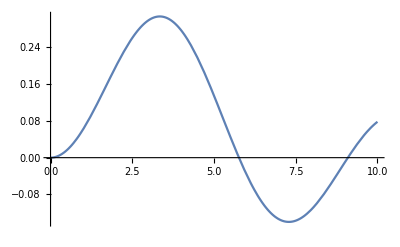

```mathematica
Plot[SphericalBesselJ[2, x], {x, 0, 10}]
```

```mathematica
FindRoot[SphericalBesselJ[2, x], {x, 5, 6}]
```

{x→5.76346}

```mathematica
k2=n/a*5.763459196894549;
Solve[ π^2/a^2(n + Subscript[δ, l])^2 == k2^2, Subscript[δ, l]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{δ_l→-2.83457 n},{δ_l→0.834566 n}}

c) A magnetic field is applied, of strength B. Find the first-order correction to the energy levels.

The wavefunction is: 

ψ0 = A * BJ_0((BJ_0 Zero(r)*r)/a)Y_00(θ, ϕ)

Let the Z direction of the system be defined as the direction of the B field because of spherical symmetry, this is valid. 

The perturbation: 	H1=e/(2 m_e c) B·L 		--> 		H1=e/(2 m_e c) BL_z 	

L_z |ψ0⟩  = ℏ m_l |ψ0⟩ 

The first order correction is : 	 ⟨ψ0|H1 |ψ0⟩  = e/(2 m_e c) B ( ℏ m_l)

The first order correction, E1, is eℏ/(2 m_e c) B m_l. 

This looks similar to a Zeeman shift and you can see that the shift for the m_l=0 state is 0, and the m_l= 1 and m_l= -1, the shift is equal and opposite. 

(Citation: Townsend pg 411 )

First order correction to the energy: E1 = eℏ/(2 m_e c) B m_l

d) Two more identical particles are added. What is the energy and degeneracy of the first excited state for B = 0?

The particles are bosons, and so more than one can occupy the same state, so we have 2 in the ground state and on in the first excited state. 

From a, we know that the energies are as follows for the three particles:			E_(nl=0) = (π^2 ℏ^2)/(2 M a^2)(n + δ_l)^2 

	E_00 = (π^2 ℏ^2)/(2 M a^2)(1 + δ_0)^2  - Ground state
	E_00 = (π^2 ℏ^2)/(2 M a^2)(1 + δ_0)^2 - Ground state
	E_11 = (π^2 ℏ^2)/(2 M a^2)(1 + δ_1)^2 - First excited state  	(the first excited state is n=1, l =1) (Townsend 367)

Energy of the first excited state: E1 = 2*E_00+ E_11 = (π^2 ℏ^2)/(2 M a^2)(2((1 + δ_0)^2+(1 + δ_1)^2)

There is a three fold degenercy becuase any two can be in the ground state while the other is in the excited state, so there are three ways to do it. 

(Citation: Townsend 10.4 )

First excited state energy: E1 = (π^2 ℏ^2)/(2 M a^2)(2((1 + δ_0)^2+(1 + δ_1)^2)
Degeneracy = 3

## 3) A Rb atom in its ground (5s) state is place in an electric field, adding a term V = e x Ε to the Rb Hamiltonian. Ignore spin.

a) With the field on, the |5s⟩ state is changed to 5s + ∑_(m,l) ϵ_lm 5l m. What are the values of l and m and why?

E ∝ H0 + V  ∝ H0 + (5sx5s + 5sx5 p_(ml = 1) +5sx5 p_(ml = 0) +5sx5 p_(ml = 0) +5sx5 p_(ml = -1) +∑_m 5sx5 d_ml + ...) 

5sx5l  = 5s Π^†Π x Π^†Π5l  = λ_(5s)λ_x λ_(5l) 5sx5l = 1* (-1) λ_(5l)5sx5l 

If	 λ_(5l) = 1, 	then ⟨5s|x |5l⟩   = - ⟨5s|x |5l⟩  , 	Thus,  ⟨5s|x |5l⟩  = 0,		

so we need that λ_(5l) = -1, and  we can see that the l states need to be of odd parity, and thus l = 1, neglecting terms higher that l = 2. 

In addition, the m_l = 0 term is not allowed. 

Thus:  l = 0 		m_l = 1, -1

(Citation: Townsend 7.10)

l = 0 		m_l = 1, -1

```mathematica
(* Taken from below, extra proof that m= 0 case is zero *)

Subscript[ϵ, 10] = e*Ε *Integrate[Subscript[P, 5, 1][r, 1]*Conjugate[SphericalHarmonicY[1, 0, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 0][r, 1]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
```

0

b) Use perturbation theory to give a formula for ϵ_lm in terms of relevant matrix elements of V and unperturbed Rb energy levels.

Following the procedure in (Townsend 11.1 ): 

H = H0 + H1 , H0 is the unperturbed and H1 is the perturbed Hamiltonian. 

ψ_n = ϕ_n^(0) + λ∑_(k≠n) ϕ_n^(0) (ϕ_k^(0)H1 ϕ_k^(0))/(E_n^(0)- E_k^(0)) + O(λ)^2    	(Townsend 11.23)

So,	 ϵ_lm = (ϕ_k^(0)H1 ϕ_k^(0))/(E_n^(0)- E_k^(0)) , 		ϵ_lm =  (5p m_lH1 5s 0)/(E_(5s 0)- E_(5p m_l)), 	Where m_l = -1, 1 . 

V = e x Ε = H1

Thus: 	ϵ_lm =  e Ε (5p m_lx 5s 0)/(E_(5s 0)- E_(5p m_l)), 	Where m_l = -1, 1 . 

(Citation: Townsend Chapter 11, 11.1, and Prof Walker Perturbation theory notebook)

ϵ_lm =  e Ε (5p m_lx 5s 0)/(E_(5s 0)- E_(5p m_l)), 	Where m_l = -1,  1

c) Calculate the induced dipole moment    - e 〈x〉.

Induced dipole moment: 	μ =  -e ⟨x⟩  =  -e  ψx ψ 

ϵ_lm =  e Ε (5p m_lx 5s 0)/(E_(5s 0)- E_(5p m_l))

From (11.23) 		ψ= 5s 0 + ϵ_(1-1)5p -1  + ϵ_10 5p 0  + ϵ_11 5p 1  

 Set E_(5s 0)as the zero of the system, E_(5s 0) = ,	 E_(5p m_l)= E_p

 Express x in terms of theta and phi: x = r*Cos[ϕ] Sin[θ]
 
 Find the Epsilons:

 E_p= 1.56 eV (NIST Energy level data)
 
 ϵ_(1-1) = e Ε (5p -1x 5s 0)/-E_p	 = 	(15 e Ε)/-E_p
 
ϵ_11 = e Ε (5p 1x 5s 0)/-E_p	 = 	(-15 e Ε)/-E_p

```mathematica
Subscript[P, n_, l_][r_, Z_]:=√Z*Subscript[P, n, l][Z*r];
```

```mathematica
Subscript[ϵ, 1-1] = e*Ε *Integrate[Subscript[P, 5, 1][r, 1]*Conjugate[SphericalHarmonicY[1, -1, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 0][r, 1]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
Subscript[ϵ, 11] = e*Ε *Integrate[Subscript[P, 5, 1][r, 1]*Conjugate[SphericalHarmonicY[1, 1, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 0][r, 1]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
```

15 e Ε

-15 e Ε

μ =  -e ⟨x⟩  =  -e  ψx ψ 

ψ= 5s 0 + ϵ_(1-1)5p -1  + ϵ_11 5p 1  
ψ= 5s 0 + ϵ_(1-1)5p -1  + ϵ_11 5p 1  

ψx ψ  = 5s 0x 5s 0  + ϵ_(1-1)5s 0x 5p -1  + ϵ_115s 0x 5p 1  +  ϵ_(1-1)5p -1x 5s 0  +  ϵ_(1-1)ϵ_(1-1)5p -1x 5p -1  +  ϵ_(1-1)ϵ_115p -1x 5p 1 + ϵ_115p 1x 5s 0  + ϵ_11ϵ_(1-1)5p 1x 5p -1  + ϵ_11 ϵ_115p 1x 5p 1 

ψx ψ  = 0 + ϵ_(1-1)5s 0x 5p -1  + ϵ_115s 0x 5p 1  +  ϵ_(1-1)5p -1x 5s 0  +  ϵ_(1-1)ϵ_(1-1)(0)  +  ϵ_(1-1)ϵ_11(0)+ ϵ_115p 1x 5s 0  + ϵ_11ϵ_(1-1)(0) + ϵ_11 ϵ_11(0)

```mathematica
ExptX1 = Subscript[ϵ, 1-1]/-Ep*Integrate[Subscript[P, 5, 0][r, 1]*Conjugate[SphericalHarmonicY[0, 0, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 01][r, 1]*SphericalHarmonicY[1, -1, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
ExptX2 = Subscript[ϵ, 11]/-Ep*Integrate[Subscript[P, 5, 0][r, 1]*Conjugate[SphericalHarmonicY[0, 0, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 1][r, 1]*SphericalHarmonicY[1, 1, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
ExptX3 = Subscript[ϵ, 1-1]/-Ep*Integrate[Subscript[P, 5, 1][r, 1]*Conjugate[SphericalHarmonicY[1, -1, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 0][r, 1]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
ExptX4 = Subscript[ϵ, 11]/-Ep*Integrate[Subscript[P, 5, 1][r, 1]*Conjugate[SphericalHarmonicY[1, 1, θ, ϕ]]*r*Cos[ϕ]*Sin[θ]*Subscript[P, 5, 0][r, 1]*SphericalHarmonicY[0, 0, θ, ϕ]*Sin[θ], {r, 0, ∞}, {ϕ, 0, 2*π}, {θ, 0, π}]
```

-(225 e Ε)/Ep

-(225 e Ε)/Ep

-(225 e Ε)/Ep

«1 more identical outputs»

```mathematica
ExptX = ExptX1 + ExptX2 + ExptX3 + ExptX4
```

-(900 e Ε)/Ep

ψx ψ  = -(900 e Ε)/Ep

μ =  -e ⟨x⟩  =  -e  ψx ψ  =  - e*( -(900 e Ε)/Ep )

```mathematica
900/1.56
```

576.923

μ=  (e^2 Ε)/Ep,   E_p= 1.56 eV  = 0.05732895 Hartrees

```mathematica
μ=  (e^2 Ε)/Ep
```

μ=  (e^2 Ε)/Ep, 	Where E_p  = 0.0573 Hartrees

## 4)

What is || 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u||, where S̄ = OverBar[S_1]  + OverBar[S_2]  + OverBar[S_3]  is the total spin opera-
tor of the 3 electrons in the Li atom? You can probably figure out the answer from the NIST tables, but use your knowledge of Li wavefunctions and spin operators to prove it.

|| 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u||, 	S̄ = OverBar[S_1]  + OverBar[S_2]  + OverBar[S_3]  

ABC + CAB + BCA - ACB -CBA - BAC

||| 2 s d; 1 s u; 2 s u||⟩ =  1/Sqrt[6]( 2 s d; 1 s u; 2 s u  +  2 s u; 2 s d; 1 s u +   1 s u; 2 s u; 2 s d  -  2 s d;  2 s u; 1 s u -   2 s u; 1 s u; 2 s d -   1 s u; 2 s d; 2 s u)

S^2 = (s1 +s2+s3)^2 = (s1 +s2+s3) (s1 +s2+s3) = s1^2 + s1s2 + s1s3 + s2s1 + s2^2+s2s3 + s3s1 + s3s2 + s3^2

We don’t know how to act s1s2 onto the state vector without altering it. I tried to use the trick that we used in class where we rewrite s1s2 in terms of the operators that the state vectors are eigenstates of:

Example: 	 s = s1 + s2	s^2 = s1^2 + s2^2 + 2  s1s2 	s1s2 =1/2 ( s^2 - s1^2 - s2^2 )

This is the trick that I try to use below to rewrite the operator in terms of operators that we know how to act on the state without changing the state: 

In order to do so, Define s12 = S1 + S2, 

s1s2=(s12^2-s1^2-s2^2)/2,	s1s3=(s13^2-s1^2-s3^2)/2, 	s2s3=(s23^2-s2^2-s3^2)/2, 

S^2 =  s1^2 + (s12^2-s1^2-s2^2)/2 + (s13^2-s1^2-s3^2)/2 + (s12^2-s1^2-s2^2)/2 + s2^2+(s23^2-s2^2-s3^2)/2 + (s13^2-s1^2-s3^2)/2 + (s23^2-s2^2-s3^2)/2 + s3^2

S^2 =  s1^2 + s12^2-s1^2-s2^2 + s2^2+ s13^2-s1^2-s3^2 + s23^2-s2^2-s3^2 + s3^2

S^2 =   s12^2+ s13^2-s1^2-s3^2 + s23^2-s2^2

Following angular momentum rules: 

s1^2  2 s d; 1 s u; 2 s u = ℏ^2 (1/2(1/2+1)) 2 s d; 1 s u; 2 s u  = 3/4 ℏ^2  2 s d; 1 s u; 2 s u
s12^2 2 s d; 1 s u; 2 s u = (s1 + s2)^2 2 s d; 1 s u; 2 s u =  ℏ^2 (1(1+1)) 2 s d; 1 s u; 2 s u = 2 ℏ^2  2 s d; 1 s u; 2 s u 

S^2 2 s d; 1 s u; 2 s u = (0) ℏ^2 + 2 ℏ^2 + (0)ℏ^2 -3/4 ℏ^2-3/4 ℏ^2-3/4 ℏ^2 = -ℏ^2/4

The other terms follow similarly and you get: 

|| 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u|| =  6 ( -ℏ^2/4) = -6/4 ℏ^2

(Citation: Slater notebook and Townsend ch 3  )

|| 2 s d; 1 s u; 2 s u||(Ŝ)^2|| 2 s d; 1 s u; 2 s u|| = -6/4 ℏ^2